```mathematica
(* Effective ringflip hopping strength calculator for the busy consumer 
 The Model:

 H = Subscript[J, 0]/2 ∑_i Subscript[Z, i] Subscript[Z, i]* +  (3OT I forgot) + ∑_hexagons  {Subscript[J, ring]+ Subscript[ξ, 1]∑_(ij) Subscript[n, i] Subscript[n, j] + Subscript[ξ, 2A]∑_Subscript[((ij)), A] Subscript[n, i] Subscript[n, j] + Subscript[ξ, 2B]∑_Subscript[((ij)), JzB] Subscript[n, i] Subscript[n, j] + Subscript[ξ, 3]∑_(((ij))) Subscript[n, i] Subscript[n, j]} O
+ h.c.

All constants are complex in general. However, symmetry requires Subscript[J, 0] and Subscript[ξ, 3] to be real. If inversion symmetry is restored, all coupling constants become real.
*)
```

```mathematica
U1[a_,b_] := 1/(a+3b)(1/(a+b)^2+1/(4 b^2)+2/(2b(a+b)))+1/(a+b)^3
U2[a_,b_] := 1/(2b(a+b)^2)+2/(4 b^2(a+b))
U3[a_,b_] := 1/(4 b^2(a+b))
U4 = 1/(JzA+JzB)^3
U5 = 1/(2JzA JzB(JzA+JzB)^2)
```

1/(JzA+JzB)^3

1/(2 JzA JzB (JzA+JzB)^2)

```mathematica
I2 = (3 KA KB)/(2(JzA+JzB))
Jring4O = +21/8 JA JB U5 JzB KA KA+21/8 JA JB U5 JzA KB KB+3/2 JA JA U2[JzA,JzB] KB KB+3/2 JA JA U3[JzA,JzB] KA KB+3/2 JB JB U2[JzB,JzA] KA KA+3/2 JB JB U3[JzB,JzA] KA KB-3/8 JA JB U5 JzB KB KB-3/8 JA JB U5 JzA KA KA-3/4 JA JA U1[JzA,JzB] KB KB-3/4 JA JA U3[JzA,JzB] KB KB-3/4 JB JB U1[JzB,JzA] KA KA-3/4 JB JB U3[JzB,JzA] KA KA-3/4 JA JB U4 KB KB-3/4 JA JB U4 KA KA-3/2 JA JA U1[JzA,JzB] KA KB-3/2 JB JB U1[JzB,JzA] KA KB-6 JA JA U2[JzA,JzB] KA KA-6 JB JB U2[JzB,JzA] KB KB-3 JA JA U1[JzA,JzB] KA KA-3 JA JA U3[JzA,JzB] KA KA-3 JB JB U1[JzB,JzA] KB KB-3 JB JB U3[JzB,JzA] KB KB+3/2 JA JB U5 JzB KA KB+3/2 JA JB U5 JzA KA KB+3 JA JB U4 KA KB+I(+21/8 JA JB U5 JzB KA KA √3-21/8 JA JB U5 JzA KB KB √3+3/2 JA JA U2[JzA,JzB] KB KB √3-3/2 JA JA U3[JzA,JzB] KA KB √3-3/2 JB JB U2[JzB,JzA] KA KA √3+3/2 JB JB U3[JzB,JzA] KA KB √3+3/8 JA JB U5 JzB KB KB √3-3/8 JA JB U5 JzA KA KA √3-3/4 JA JA U1[JzA,JzB] KB KB √3-3/4 JA JA U3[JzA,JzB] KB KB √3+3/4 JB JB U1[JzB,JzA] KA KA √3+3/4 JB JB U3[JzB,JzA] KA KA √3+3/4 JA JB U4 KB KB √3-3/4 JA JB U4 KA KA √3+3/2 JA JA U1[JzA,JzB] KA KB √3-3/2 JB JB U1[JzB,JzA] KA KB √3);
ξ1 = -6 JB JB U1[JzB,JzA] KA KB-12 JB JB U2[JzB,JzA] KA KB-6 JB JB U3[JzB,JzA] KA KB-3 JA JA U1[JzA,JzB] KA KB-6 JA JA U2[JzA,JzB] KA KB-3 JA JA U3[JzA,JzB] KA KB+3 JB JB U1[JzB,JzA] KA KB+6 JB JB U2[JzB,JzA] KA KB+3 JB JB U3[JzB,JzA] KA KB + I(
+3 JA JA U1[JzA,JzB] KA KB √3+6 JA JA U2[JzA,JzB] KA KB √3+3 JA JA U3[JzA,JzB] KA KB √3-3 JB JB U1[JzB,JzA] KA KB √3-6 JB JB U2[JzB,JzA] KA KB √3-3 JB JB U3[JzB,JzA] KA KB √3
)
ξ3 = +12 JA JB U4 KA KB+42 JA JB U5 JzA KA KB+42 JA JB U5 JzB KA KB
ξ2A = +6 JA JB U4 KA KA+21 JA JB U5 JzA KA KA+21 JA JB U5 JzB KA KA-3 JA JB U4 KA KA-21/2 JA JB U5 JzA KA KA-21/2 JA JB U5 JzB KA KA+3 JB JB U1[JzB,JzA] KA KA+6 JB JB U2[JzB,JzA] KA KA+3 JB JB U3[JzB,JzA] KA KA + I(
+3 JA JB U4 KA KA √3+21/2 JA JB U5 JzA KA KA √3+21/2 JA JB U5 JzB KA KA √3-3 JB JB U1[JzB,JzA] KA KA √3-6 JB JB U2[JzB,JzA] KA KA √3-3 JB JB U3[JzB,JzA] KA KA √3
)
ξ2B = +6 JA JA U1[JzA,JzB] KB KB+6 JA JA U3[JzA,JzB] KB KB+12 JA JA U2[JzA,JzB] KB KB+21/2 JA JB U5 JzA KB KB+21/2 JA JB U5 JzB KB KB+3 JA JB U4 KB KB-3 JA JA U1[JzA,JzB] KB KB-3 JA JA U3[JzA,JzB] KB KB-6 JA JA U2[JzA,JzB] KB KB + I(
-21/2 JA JB U5 JzA KB KB √3-21/2 JA JB U5 JzB KB KB √3-3 JA JB U4 KB KB √3+3 JA JA U1[JzA,JzB] KB KB √3+3 JA JA U3[JzA,JzB] KB KB √3+6 JA JA U2[JzA,JzB] KB KB √3)
```

(3 KA KB)/(2 (JzA+JzB))

-(3 JB^2 KA KB)/(4 JzA^2 (JzA+JzB))-(3 JA^2 KA KB)/(4 JzB^2 (JzA+JzB))-6 JB^2 (1/(2 JzA (JzA+JzB)^2)+1/(2 JzA^2 (JzA+JzB))) KA KB-6 JA^2 (1/(2 JzB (JzA+JzB)^2)+1/(2 JzB^2 (JzA+JzB))) KA KB-3 JB^2 (1/(JzA+JzB)^3+(1/(4 JzA^2)+1/(JzA+JzB)^2+1/(JzA (JzA+JzB)))/(3 JzA+JzB)) KA KB-3 JA^2 (1/(JzA+JzB)^3+(1/(4 JzB^2)+1/(JzA+JzB)^2+1/(JzB (JzA+JzB)))/(JzA+3 JzB)) KA KB+ⅈ (-(3 √3 JB^2 KA KB)/(4 JzA^2 (JzA+JzB))+(3 √3 JA^2 KA KB)/(4 JzB^2 (JzA+JzB))-6 √3 JB^2 (1/(2 JzA (JzA+JzB)^2)+1/(2 JzA^2 (JzA+JzB))) KA KB+6 √3 JA^2 (1/(2 JzB (JzA+JzB)^2)+1/(2 JzB^2 (JzA+JzB))) KA KB-3 √3 JB^2 (1/(JzA+JzB)^3+(1/(4 JzA^2)+1/(JzA+JzB)^2+1/(JzA (JzA+JzB)))/(3 JzA+JzB)) KA KB+3 √3 JA^2 (1/(JzA+JzB)^3+(1/(4 JzB^2)+1/(JzA+JzB)^2+1/(JzB (JzA+JzB)))/(JzA+3 JzB)) KA KB)

(12 JA JB KA KB)/(JzA+JzB)^3+(21 JA JB KA KB)/(JzA (JzA+JzB)^2)+(21 JA JB KA KB)/(JzB (JzA+JzB)^2)

(3 JA JB KA^2)/(JzA+JzB)^3+(21 JA JB KA^2)/(4 JzA (JzA+JzB)^2)+(21 JA JB KA^2)/(4 JzB (JzA+JzB)^2)+(3 JB^2 KA^2)/(4 JzA^2 (JzA+JzB))+6 JB^2 (1/(2 JzA (JzA+JzB)^2)+1/(2 JzA^2 (JzA+JzB))) KA^2+3 JB^2 (1/(JzA+JzB)^3+(1/(4 JzA^2)+1/(JzA+JzB)^2+1/(JzA (JzA+JzB)))/(3 JzA+JzB)) KA^2+ⅈ ((3 √3 JA JB KA^2)/(JzA+JzB)^3+(21 √3 JA JB KA^2)/(4 JzA (JzA+JzB)^2)+(21 √3 JA JB KA^2)/(4 JzB (JzA+JzB)^2)-(3 √3 JB^2 KA^2)/(4 JzA^2 (JzA+JzB))-6 √3 JB^2 (1/(2 JzA (JzA+JzB)^2)+1/(2 JzA^2 (JzA+JzB))) KA^2-3 √3 JB^2 (1/(JzA+JzB)^3+(1/(4 JzA^2)+1/(JzA+JzB)^2+1/(JzA (JzA+JzB)))/(3 JzA+JzB)) KA^2)

(3 JA JB KB^2)/(JzA+JzB)^3+(21 JA JB KB^2)/(4 JzA (JzA+JzB)^2)+(21 JA JB KB^2)/(4 JzB (JzA+JzB)^2)+(3 JA^2 KB^2)/(4 JzB^2 (JzA+JzB))+6 JA^2 (1/(2 JzB (JzA+JzB)^2)+1/(2 JzB^2 (JzA+JzB))) KB^2+3 JA^2 (1/(JzA+JzB)^3+(1/(4 JzB^2)+1/(JzA+JzB)^2+1/(JzB (JzA+JzB)))/(JzA+3 JzB)) KB^2+ⅈ (-(3 √3 JA JB KB^2)/(JzA+JzB)^3-(21 √3 JA JB KB^2)/(4 JzA (JzA+JzB)^2)-(21 √3 JA JB KB^2)/(4 JzB (JzA+JzB)^2)+(3 √3 JA^2 KB^2)/(4 JzB^2 (JzA+JzB))+6 √3 JA^2 (1/(2 JzB (JzA+JzB)^2)+1/(2 JzB^2 (JzA+JzB))) KB^2+3 √3 JA^2 (1/(JzA+JzB)^3+(1/(4 JzB^2)+1/(JzA+JzB)^2+1/(JzB (JzA+JzB)))/(JzA+3 JzB)) KB^2)

```mathematica
g = -Evaluate[Jring4O]+(3 JA^3)/(4 JzB^2)+(3 JB^3)/(4 JzA^2) - (6 JA^2 JB^2)/(8 JzB^3)- (6 JA^2 JB^2)/(8 JzA^3) // FullSimplify
ξ1   = Evaluate[ξ1] // FullSimplify
ξ2A = Evaluate[ξ2A] // FullSimplify
ξ2B = Evaluate[ξ2B] // FullSimplify
ξ3   = Evaluate[ξ3] // FullSimplify
```

1/(16 JzA^3 JzB^3 (JzA+JzB)^3)3 (4 JA^3 JzA^3 JzB (JzA+JzB)^3+JA JB JzA^2 JzB^2 ((1+ⅈ √3) (JzA^2-2 JzA JzB-7 JzB^2) KA^2-4 (JzA^2+6 JzA JzB+JzB^2) KA KB+ⅈ (ⅈ+√3) (7 JzA^2+2 JzA JzB-JzB^2) KB^2)+2 JB^2 JzA JzB^3 (2 JB (JzA+JzB)^3+ⅈ (ⅈ+√3) JzB (3 JzA+JzB) KA^2+(2+2 ⅈ √3) JzA (3 JzA+JzB) KA KB+4 (8 JzA^2+9 JzA JzB+3 JzB^2) KB^2)+2 JA^2 (-2 JB^2 (JzA+JzB)^4 (JzA^2-JzA JzB+JzB^2)+JzA^3 JzB (4 (3 JzA^2+9 JzA JzB+8 JzB^2) KA^2+(2-2 ⅈ √3) JzB (JzA+3 JzB) KA KB+(-1-ⅈ √3) JzA (JzA+3 JzB) KB^2)))

1/(2 JzA^2 JzB^2 (JzA+JzB)^3)3 ⅈ (-((-ⅈ+√3) JB^2 JzB^2 (8 JzA^2+9 JzA JzB+3 JzB^2))+(ⅈ+√3) JA^2 JzA^2 (3 JzA^2+9 JzA JzB+8 JzB^2)) KA KB

1/(4 JzA^2 JzB (JzA+JzB)^3)3 JB ((2-2 ⅈ √3) JB JzB (8 JzA^2+9 JzA JzB+3 JzB^2)+(1+ⅈ √3) JA JzA (7 JzA^2+18 JzA JzB+7 JzB^2)) KA^2

1/(4 JzA JzB^2 (JzA+JzB)^3)3 JA ((1-ⅈ √3) JB JzB (7 JzA^2+18 JzA JzB+7 JzB^2)+(2+2 ⅈ √3) JA JzA (3 JzA^2+9 JzA JzB+8 JzB^2)) KB^2

(3 JA JB (7 JzA^2+18 JzA JzB+7 JzB^2) KA KB)/(JzA JzB (JzA+JzB)^3)

```mathematica
Manipulate[
Plot[Evaluate[{Re[g],Im[g],-Re[ξ2A]} /.{JzA->1, JzB->α , KA->k , KB->k α, JA->J ,JB->J α}],{α,0.1,1},
PlotLegends->{ "real","imag","ξ3"}
],
{k,0,1},{J,-1,1}]
```

```mathematica
gSimpl = g/.{JzA->1, JzB->α , KA->k, KB->α k, JA->J,JB->α J}
FullSimplify[Arg[gSimpl]]
```

1/(16 α^3 (1+α)^3)3 (4 J^3 α (1+α)^3+J^2 α^3 ((1+ⅈ √3) k^2 (1-2 α-7 α^2)+ⅈ (ⅈ+√3) k^2 α^2 (7+2 α-α^2)-4 k^2 α (1+6 α+α^2))+2 J^2 α^5 (2 J α (1+α)^3+(2+2 ⅈ √3) k^2 α (3+α)+ⅈ (ⅈ+√3) k^2 α (3+α)+4 k^2 α^2 (8+9 α+3 α^2))+2 J^2 (-2 J^2 α^2 (1+α)^4 (1-α+α^2)+α ((-1-ⅈ √3) k^2 α^2 (1+3 α)+(2-2 ⅈ √3) k^2 α^2 (1+3 α)+4 k^2 (3+9 α+8 α^2))))

Arg[1/(α^2 (1+α)^2)J^2 (-4 J^2 α (1+α)^3 (1+(-1+α) α)+4 J (1+α (2+α+α^4+2 α^5+α^6))+k^2 (24+α (48+α (19-5 ⅈ √3+α (-19-15 ⅈ √3+α (-19+15 ⅈ √3+α (19+5 ⅈ √3+24 α (2+α))))))))]

```mathematica
rA = ξ2A/ξ1 /.{JzA->Jz, JzB->Jz α , KA->k, KB->α k, JA->J,JB->α J} //Simplify
rB = ξ2B/ξ1 /.{JzA->Jz, JzB->Jz α , KA->k, KB->α k, JA->J,JB->α J} //Simplify
r3 = ξ3/ξ1 /.{JzA->Jz, JzB->Jz α , KA->k, KB->α k, JA->J,JB->α J} //Simplify
```

-(ⅈ α ((2-2 ⅈ √3) α^2 (8+9 α+3 α^2)+(1+ⅈ √3) (7+18 α+7 α^2)))/(2 (-((-ⅈ+√3) α^4 (8+9 α+3 α^2))+(ⅈ+√3) (3+9 α+8 α^2)))

-(ⅈ α ((1-ⅈ √3) α^2 (7+18 α+7 α^2)+(2+2 ⅈ √3) (3+9 α+8 α^2)))/(2 (-((-ⅈ+√3) α^4 (8+9 α+3 α^2))+(ⅈ+√3) (3+9 α+8 α^2)))

(2 ⅈ α^2 (7+18 α+7 α^2))/(-3 (ⅈ+√3)-9 (ⅈ+√3) α-8 (ⅈ+√3) α^2+8 (-ⅈ+√3) α^4+9 (-ⅈ+√3) α^5+3 (-ⅈ+√3) α^6)

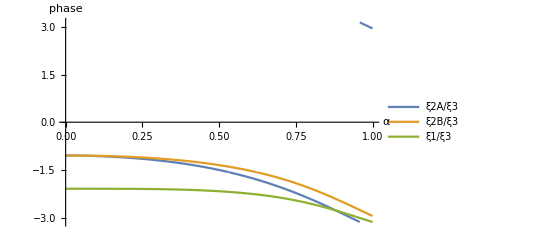

```mathematica
Plot[Evaluate[Arg/@{rA,rB,r3} /.{Jz->1}],{α,0,1},
PlotLegends->{ "ξ2A/ξ3","ξ2B/ξ3","ξ1/ξ3"},PlotRange->All,AxesLabel->{α,"phase"}]
```

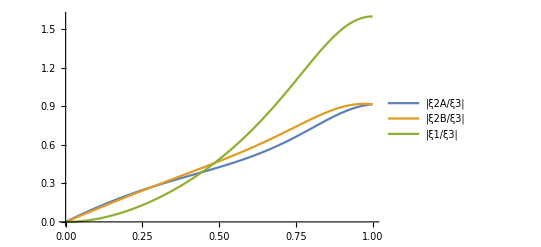

```mathematica
Plot[Evaluate[Abs/@{rA,rB,r3} /.{Jz->1}],{α,0,1},
PlotLegends->{ "|ξ2A/ξ3|","|ξ2B/ξ3|","|ξ1/ξ3|"},PlotRange->All]
```

```mathematica
Plot[ξ3,
```